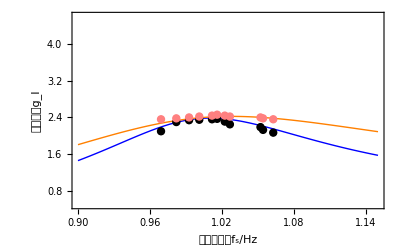

```mathematica
Clear[w,Rl,g,Lp,Ls,Cp,Cs,ghudao,k,x];
Lp=Ls=52×10^-6;
Cp=Cs=220×10^-9;
Uin=1;
fr=47050;

k=0.157;
M=√(Lp×Ls)×k;
Rp=0.05;
Rs=0.05;
w=x*fr;
s=2*π*w*I;
R1=Rp+(s*Lp+1/(s*Cp));
R2=Rs+Rl+(s*Ls+1/(s*Cs));
Rf=(s*M)^2/R2;

Ip=Uin/(R1+Rf);
Is=s*M/R2*Ip;

gz=Is*Rl/Ip;

I1=72/gz;
I1=Sqrt[ComplexExpand[Re[FullSimplify[I1]]]^2+ComplexExpand[Im[FullSimplify[I1]]]^2];
gzzz=72/I1;

a=0.8;
b=0.7;
p1=Plot[Evaluate@Table[gzzz,{Rl,3,3,1}],{x,0.9,1.15},
PlotRange->{0,3},
Frame->True,
FrameLabel->{Style["(:5f52:4e00:5316:9891:7387f)_s/Hz",Black],Style["(:7535:6d41:589e:76cag)_I",Black]},
PlotLegends->Placed[{"R_L=3Ω(仿真)"},{a,b}],

PlotStyle->{{Blue,Thick},{Blue,Thick},{Purple,Thick},{Pink,Thick},{Orange,Thick}}];


p2=Plot[Evaluate@Table[gzzz,{Rl,5,5,1}],{x,0.9,1.15},
PlotRange->{0,3},
Frame->True,
FrameLabel->{Style["(:5f52:4e00:5316:9891:7387f)_s/Hz",Black],Style["(:7535:6d41:589e:76cag)_I",Black]},
PlotLegends->Placed[{"R_L=5Ω(仿真)"},{a,b}],
(*PlotLabel->Style["(:4e0d:540c:8d1f:8f7d:7535:963bR)_L下，(:4e92:5bfc:589e:76caG)_h(:4e0e:9891:7387f)_s的关系",Black,Bold],*)
PlotStyle->{{Orange,Thick},{Blue,Thick},{Purple,Thick},{Pink,Thick},{Orange,Thick}}];

dist3=Import["D:/data/dianliu3.csv"];
p3=ListPlot[dist3,InterpolationOrder->2,Mesh->Full,
PlotLegends->Placed[{"   R_L=3Ω(实测)"},{a,b}],
PlotStyle->{Black,Thick}];

dist4=Import["D:/data/dianliu5.csv"];
p4=ListPlot[dist4,InterpolationOrder->2,Mesh->Full,
PlotLegends->Placed[{"   R_L=5Ω(实测)"},{a,b}],
Frame->True,
DataRange->{0,3},

PlotStyle->{Pink,Thick}];


Show[p1,p2,p3,p4,PlotRange->{0.5,4.6}]
```